```mathematica
h = 6.6261963*10^-35 (*Jerk-sh*)
```

6.6262×10^-35

```mathematica
k=1.6021917*10^-25 (*Jrk/keV*)
```

1.60219×10^-25

```mathematica
c = 299.792458 (*cm/sh*)
```

299.792

```mathematica
B[ν_,T_]:= (2 k^4 ν^3)/(h^3c^2) 1/(Exp[ν/(T)]-1) (*Clark,JCP 70,no.2 1987,p 316*)
```

```mathematica
OpacData = Import["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AluminumRefinedgroups2.csv"]
```

{{0.001,1.×10^10,1.×10^10},{0.001229,1.×10^10,1.×10^10},{0.0015104,1.×10^10,1.×10^10},{0.0018562,1.×10^10,1.×10^10},{0.0022812,1.×10^10,1.×10^10},{0.0028036,1.×10^10,1.×10^10},{0.0034455,1.×10^10,1.×10^10},{0.0042344,1.×10^10,1.×10^10},{0.005204,1.×10^10,1.×10^10},{0.0063956,1.×10^10,1.×10^10},{0.00786,1.×10^10,1.×10^10},{0.0096598,1.×10^10,1.×10^10},{0.011872,1.×10^10,1.×10^10},{0.01459,1.×10^10,1.×10^10},{0.017931,1.×10^10,1.×10^10},{0.022036,8932.1,8932.6},{0.027082,8561.5,8569.},{0.033283,7307.1,7334.8},{0.040904,5610.5,5655.9},{0.05027,3984.1,4031.},{0.06178,2671.3,2710.5},{0.075926,1742.3,1769.8},{0.093311,1174.7,1184.4},{0.11468,778.38,792.36},{0.14093,497.78,506.05},{0.17321,317.6,322.98},{0.21286,202.84,206.18},{0.2616,172.36,209.98},{0.32151,108.33,122.94},{0.39512,75.001,75.79},{0.48559,48.333,49.048},{0.59678,30.697,31.1},{0.73343,19.245,19.467},{0.90136,11.878,11.961},{1.,12.05,11.866},{1.014,11.67,11.486},{1.0281,11.3,11.116},{1.0425,10.942,10.758},{1.057,10.595,10.41},{1.0718,10.256,10.071},{1.0867,9.925,9.7402},{1.1019,9.6008,9.4159},{1.1173,9.2827,9.0977},{1.1329,8.9699,8.7849},{1.1487,8.6619,8.4769},{1.1647,8.365,8.1799},{1.181,8.0855,7.9002},{1.1975,7.8204,7.635},{1.2142,7.567,7.3815},{1.2311,7.3233,7.1377},{1.2483,7.0879,6.9022},{1.2658,6.8597,6.6739},{1.2834,6.6379,6.452},{1.3013,6.4231,6.2371},{1.3195,6.2152,6.0292},{1.3379,6.0134,5.8273},{1.3566,5.8167,5.6306},{1.3755,5.6246,5.4384},{1.3947,5.4367,5.2504},{1.4142,5.2528,5.0665},{1.434,5.0722,4.8859},{1.454,4.8954,4.709},{1.4743,4.7289,4.5424},{1.4948,4.5736,4.3869},{1.5157,4.4302,4.2434},{1.5369,4.3036,4.1166},{1.5583,4.4678,4.3104},{1.5801,6.6902,15.721},{1.6021,4.7171,4.8339},{1.6245,3.9134,3.7262},{1.6472,3.9451,3.7581},{1.6702,4.8071,4.7057},{1.6935,15.295,33.942},{1.7171,217.3,903.44},{1.7411,10.23,16.153},{1.7654,4.242,4.0975},{1.7901,3.6059,3.4195},{1.815,3.5764,3.3888},{1.8404,4.1348,3.9856},{1.8661,4.5101,4.3504},{1.8921,4.1209,3.9334},{1.9185,4.4424,4.2581},{1.9453,5.0402,4.8608},{1.9725,6.7491,6.8359},{1.9953,22.13,46.74},{2.0893,20.163,21.076},{2.1878,22.969,22.814},{2.2909,19.776,19.63},{2.3988,17.658,17.488},{2.5119,16.075,15.903},{2.6303,14.592,14.42},{2.7542,13.105,12.935},{2.884,11.607,11.438},{3.02,10.314,10.14},{3.1623,9.2226,9.0471},{3.3113,8.2327,8.0567},{3.4674,7.2935,7.1181},{3.6308,6.3952,6.2192},{3.8019,5.6533,5.4739},{3.9811,5.0419,4.8614},{4.1687,4.4922,4.3115},{4.3652,3.9725,3.7921},{4.5709,3.477,3.2964},{4.7863,3.0709,2.8884},{5.0119,2.7385,2.5555},{5.2481,2.4411,2.2581},{5.4954,2.1611,1.9785},{5.7544,1.8954,1.7128},{6.0256,1.6794,1.4958},{6.3096,1.5035,1.3199},{6.6069,1.3467,1.1632},{6.9183,1.1994,1.0162},{7.2444,1.06,0.87702},{7.5858,0.94725,0.76408},{7.9433,0.85585,0.67288},{8.3176,0.7745,0.59186},{8.7096,0.69821,0.51597},{9.1201,0.62611,0.44417},{9.5499,0.56803,0.38622},{10.701,0.41258,0.2385},{13.151,0.30609,0.13092},{16.162,0.24517,0.071433},{19.863,0.2094,0.03867},{24.411,0.18752,0.020756}}

```mathematica
tb[Z_,μ_,v_,t_,L_]:=Max[ (μ c t - Z)/(μ c - v),0]
```

```mathematica
tf[Z_,μ_,v_,t_,L_]:=Max[ (L+(μ c t - Z))/(μ c - v),0]
```

```mathematica
s[Z_,μ_,v_,t_,L_]:=Max[c*(tf[Z,μ,v,t,L]-tb[Z,μ,v,t,L]) ,0]
```

```mathematica
logspace[a_,b_,n_]:=Exp[Range[a,b,(b-a)/(n-1)]]
```

```mathematica
nbins=Dimensions[OpacData][[1]]
```

124

```mathematica
groupBounds=Table[If[i≤ nbins,OpacData[[i,1]],30],{i,1,nbins+1}]
groupWidths = Differences[groupBounds];
groupGmid=Table[GeometricMean[groupBounds[[i;;i+1]]],{i,1,nbins}];
```

{0.001,0.001229,0.0015104,0.0018562,0.0022812,0.0028036,0.0034455,0.0042344,0.005204,0.0063956,0.00786,0.0096598,0.011872,0.01459,0.017931,0.022036,0.027082,0.033283,0.040904,0.05027,0.06178,0.075926,0.093311,0.11468,0.14093,0.17321,0.21286,0.2616,0.32151,0.39512,0.48559,0.59678,0.73343,0.90136,1.,1.014,1.0281,1.0425,1.057,1.0718,1.0867,1.1019,1.1173,1.1329,1.1487,1.1647,1.181,1.1975,1.2142,1.2311,1.2483,1.2658,1.2834,1.3013,1.3195,1.3379,1.3566,1.3755,1.3947,1.4142,1.434,1.454,1.4743,1.4948,1.5157,1.5369,1.5583,1.5801,1.6021,1.6245,1.6472,1.6702,1.6935,1.7171,1.7411,1.7654,1.7901,1.815,1.8404,1.8661,1.8921,1.9185,1.9453,1.9725,1.9953,2.0893,2.1878,2.2909,2.3988,2.5119,2.6303,2.7542,2.884,3.02,3.1623,3.3113,3.4674,3.6308,3.8019,3.9811,4.1687,4.3652,4.5709,4.7863,5.0119,5.2481,5.4954,5.7544,6.0256,6.3096,6.6069,6.9183,7.2444,7.5858,7.9433,8.3176,8.7096,9.1201,9.5499,10.701,13.151,16.162,19.863,24.411,30}

```mathematica
Tval = 1 (*keV*)
```

1

```mathematica
dens = 1 /10(*g/cc*)
```

1/10

```mathematica
CForm[OpacData[[;;,3]]]
```

List(1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,
   1.e10,1.e10,8932.6,8569.,7334.8,5655.9,4031.,2710.5,1769.8,1184.4,792.36,506.05,
   322.98,206.18,209.98,122.94,75.79,49.048,31.1,19.467,11.961,11.866,11.486,11.116,
   10.758,10.41,10.071,9.7402,9.4159,9.0977,8.7849,8.4769,8.1799,7.9002,7.635,7.3815,
   7.1377,6.9022,6.6739,6.452,6.2371,6.0292,5.8273,5.6306,5.4384,5.2504,5.0665,4.8859,
   4.709,4.5424,4.3869,4.2434,4.1166,4.3104,15.721,4.8339,3.7262,3.7581,4.7057,33.942,
   903.44,16.153,4.0975,3.4195,3.3888,3.9856,4.3504,3.9334,4.2581,4.8608,6.8359,46.74,
   21.076,22.814,19.63,17.488,15.903,14.42,12.935,11.438,10.14,9.0471,8.0567,7.1181,
   6.2192,5.4739,4.8614,4.3115,3.7921,3.2964,2.8884,2.5555,2.2581,1.9785,1.7128,1.4958,
   1.3199,1.1632,1.0162,0.87702,0.76408,0.67288,0.59186,0.51597,0.44417,0.38622,0.2385,
   0.13092,0.071433,0.03867,0.020756)

```mathematica
opacsGmid=Table[Evaluate[σ[groupGmid[[j]],Tval]],{j,1,nbins}];
```

Part::pkspec1: The expression j cannot be used as a part specification.

```mathematica
pcf = Table[{OpacData[[i,3]],ν>groupBounds[[i]]&& ν≤ groupBounds[[i+1]]},{i,1,nbins}];
opacPiece = Piecewise[pcf];
```

```mathematica
opacfunc[νt_]:=opacPiece/.ν->νt
```

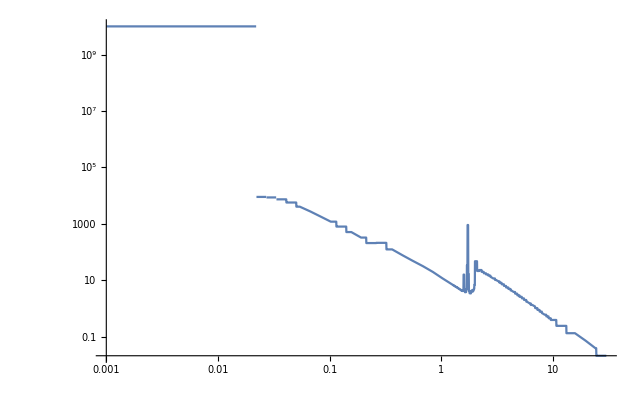

```mathematica
LogLogPlot[{opacfunc[x]+0*B[x,Tval]*200},{x,0.001,30}]
```

```mathematica
Iz[Z_,μ_,ν_,v_,t_,L_,T_,dens_]:= B[γ Dl ν, T]/(γ Dl)^3(1-Exp[-γ Dl (dens*opacfunc[ν*γ*Dl]) s[Z,μ,v,t,L]])/.{Dl-> 1-μ v/c,γ-> 1/Sqrt[(1-β^2)]}/.{β-> v/c}/.{L->L}
```

```mathematica
IzNoMult[Z_,μ_,ν_,v_,t_,L_,T_,dens_]:= B[ν, T]/(γ Dl)^3(1-Exp[-γ Dl (dens*opacfunc[ν]) s[Z,μ,v,t,L]])/.{Dl-> 1-μ v/c,γ-> 1/Sqrt[(1-β^2)]}/.{β-> v/c}/.{L->L}
```

```mathematica
spectrum=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[Iz[12,μ,T,5.994,1,4/10,Tval,dens]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->5, MaxRecursion->10,Method->"LocalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,nbins}]
```

{{0.0011086,1.23142×10^-9},{0.00136245,1.93064×10^-9},{0.0016744,2.91545×10^-9},{0.00205776,4.40164×10^-9},{0.00252895,6.64703×10^-9},{0.00310802,1.00373×10^-8},{0.00381964,1.51553×10^-8},{0.00469423,2.28803×10^-8},{0.00576912,3.45396×10^-8},{0.00709009,5.21332×10^-8},{0.00871355,7.8677×10^-8},{0.0107089,1.18718×10^-7},{0.013161,1.79053×10^-7},{0.0161745,2.70041×10^-7},{0.0198778,4.07119×10^-7},{0.0244291,6.1353×10^-7},{0.0300228,9.24077×10^-7},{0.0368973,1.39088×10^-6},{0.0453458,2.09182×10^-6},{0.0557286,3.14288×10^-6},{0.0684887,4.71634×10^-6},{0.0841708,7.0657×10^-6},{0.103445,0.0000105687},{0.127129,0.0000157713},{0.156239,0.0000234692},{0.192014,0.0000347996},{0.235975,0.0000513721},{0.290012,0.0000754328},{0.35642,0.000109897},{0.438025,0.000157495},{0.538322,0.000218853},{0.661586,0.00028829},{0.813071,0.000353768},{0.9494,0.000373838},{1.00698,0.000397004},{1.02103,0.000402515},{1.03527,0.000404835},{1.04972,0.000406677},{1.06437,0.000408361},{1.07922,0.000409884},{1.09427,0.000411198},{1.10957,0.000412315},{1.12507,0.000413188},{1.14077,0.000413788},{1.15667,0.000414089},{1.17282,0.000414116},{1.18922,0.000414047},{1.20582,0.000413978},{1.22262,0.000413864},{1.23967,0.000413659},{1.25702,0.000413341},{1.27457,0.000412898},{1.29232,0.00041224},{1.31037,0.000411395},{1.32867,0.000410406},{1.34722,0.000409233},{1.36602,0.000407866},{1.38507,0.00040626},{1.40442,0.000404408},{1.42407,0.000402305},{1.44397,0.000399925},{1.46411,0.000397235},{1.48451,0.000394383},{1.50521,0.000391592},{1.52626,0.000389},{1.54756,0.000386795},{1.56916,0.000392215},{1.59106,0.000512618},{1.61326,0.000667535},{1.63581,0.00044368},{1.65866,0.00038813},{1.68181,0.000414361},{1.70526,0.000590842},{1.72906,0.00101068},{1.75321,0.00111883},{1.77771,0.000787927},{1.80251,0.000449447},{1.82766,0.000397385},{1.85321,0.000416453},{1.87906,0.000455457},{1.90525,0.000465369},{1.93185,0.000463935},{1.95885,0.000496084},{1.98387,0.000556305},{2.04176,0.00109742},{2.13798,0.00115812},{2.23876,0.00114617},{2.34423,0.0011408},{2.4547,0.00111392},{2.57042,0.00108878},{2.69154,0.00105816},{2.81835,0.0010178},{2.95122,0.000964899},{3.09033,0.000906541},{3.23594,0.000846458},{3.38845,0.000783428},{3.54816,0.000715996},{3.71537,0.000644252},{3.89047,0.000574735},{4.07382,0.000510023},{4.26582,0.000448108},{4.46687,0.000387735},{4.67736,0.000329208},{4.8978,0.000276815},{5.12864,0.000231374},{5.37033,0.000191063},{5.62341,0.000154882},{5.88844,0.000122735},{6.16597,0.0000961847},{6.45654,0.0000748334},{6.76081,0.0000573622},{7.07947,0.0000430002},{7.41313,0.0000313829},{7.76249,0.0000226103},{8.1283,0.0000161428},{8.51134,0.0000113194},{8.91249,7.73119×10^-6},{9.33253,5.1181×10^-6},{10.1091,2.64717×10^-6},{11.8629,5.20785×10^-7},{14.579,4.00839×10^-8},{17.9172,1.69851×10^-9},{22.0199,3.54631×10^-11},{27.0616,3.1445×10^-13}}

```mathematica
Export["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNominal_124.csv",spectrum]
```

/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNominal_124.csv

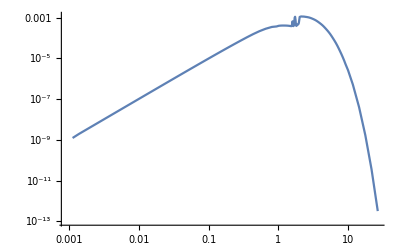

```mathematica
ListLogLogPlot[spectrum,Joined->True]
```

```mathematica
spectrumNoV=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[IzNoMult[12,μ,T,5.994,1,4/10,Tval,dens]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->5, MaxRecursion->10,Method->"LocalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,nbins}]
```

{{0.0011086,1.30504×10^-9},{0.00136245,1.97087×10^-9},{0.0016744,2.97619×10^-9},{0.00205776,4.49336×10^-9},{0.00252895,6.78551×10^-9},{0.00310802,1.02463×10^-8},{0.00381964,1.54709×10^-8},{0.00469423,2.33566×10^-8},{0.00576912,3.52584×10^-8},{0.00709009,5.32179×10^-8},{0.00871355,8.03133×10^-8},{0.0107089,1.21186×10^-7},{0.013161,1.82808×10^-7},{0.0161745,2.75647×10^-7},{0.0198778,4.15563×10^-7},{0.0244291,6.26239×10^-7},{0.0300228,9.43191×10^-7},{0.0368973,1.4196×10^-6},{0.0453458,2.13492×10^-6},{0.0557286,3.20746×10^-6},{0.0684887,4.81293×10^-6},{0.0841708,7.20982×10^-6},{0.103445,0.0000107831},{0.127129,0.0000160892},{0.156239,0.0000239385},{0.192014,0.0000354885},{0.235975,0.0000523763},{0.290012,0.0000768842},{0.35642,0.000111959},{0.438025,0.000160276},{0.538322,0.000222245},{0.661586,0.000291724},{0.813071,0.000356406},{0.9494,0.000370539},{1.00698,0.0004008},{1.02103,0.00040284},{1.03527,0.000404713},{1.04972,0.00040645},{1.06437,0.00040802},{1.07922,0.000409402},{1.09427,0.000410579},{1.10957,0.000411535},{1.12507,0.000412226},{1.14077,0.000412627},{1.15667,0.000412712},{1.17282,0.000412651},{1.18922,0.000412626},{1.20582,0.000412569},{1.22262,0.000412427},{1.23967,0.000412178},{1.25702,0.000411809},{1.27457,0.000411252},{1.29232,0.000410483},{1.31037,0.000409568},{1.32867,0.000408494},{1.34722,0.000407228},{1.36602,0.000405742},{1.38507,0.000404008},{1.40442,0.000402028},{1.42407,0.000399793},{1.44397,0.000397247},{1.46411,0.000394405},{1.48451,0.000391616},{1.50521,0.000388978},{1.52626,0.000386601},{1.54756,0.000384789},{1.56916,0.000401772},{1.59106,0.000788645},{1.61326,0.000443355},{1.63581,0.000381605},{1.65866,0.000388862},{1.68181,0.000453917},{1.70526,0.00104858},{1.72906,0.00116824},{1.75321,0.000872933},{1.77771,0.000437664},{1.80251,0.000393892},{1.82766,0.000396087},{1.85321,0.00044516},{1.87906,0.000475663},{1.90525,0.000451091},{1.93185,0.000479327},{1.95885,0.000525455},{1.98387,0.000645807},{2.04176,0.00126902},{2.13798,0.00110471},{2.23876,0.00115922},{2.34423,0.00113035},{2.4547,0.00110525},{2.57042,0.00108089},{2.69154,0.00104875},{2.81835,0.00100579},{2.95122,0.000950962},{3.09033,0.000892365},{3.23594,0.000832671},{3.38845,0.000769433},{3.54816,0.000701539},{3.71537,0.000629479},{3.89047,0.00056134},{4.07382,0.000498078},{4.26582,0.000436976},{4.46687,0.000377193},{4.67736,0.000319339},{4.8978,0.000268471},{5.12864,0.000224404},{5.37033,0.000185032},{5.62341,0.000149619},{5.88844,0.000118207},{6.16597,0.000092618},{6.45654,0.0000720567},{6.76081,0.0000551385},{7.07947,0.0000412163},{7.41313,0.0000299795},{7.76249,0.0000215903},{8.1283,0.0000154091},{8.51134,0.0000107817},{8.91249,7.33921×10^-6},{9.33253,4.83914×10^-6},{10.1091,2.52168×10^-6},{11.8629,4.82393×10^-7},{14.579,3.60115×10^-8},{17.9172,1.48442×10^-9},{22.0199,2.9916×10^-11},{27.0616,2.53675×10^-13}}

```mathematica
Export["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoDopplerNu_124.csv",spectrumNoV]
```

/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoDopplerNu_124.csv

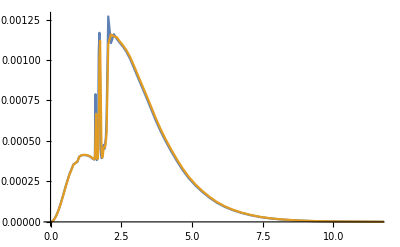

```mathematica
ListPlot[{spectrumNoV,spectrum},Joined->True]
```

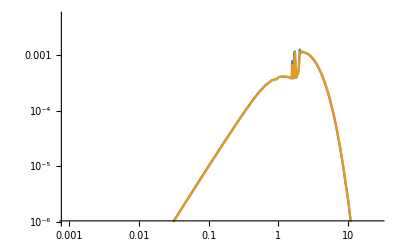

```mathematica
ListLogLogPlot[{spectrumNoV,spectrum},Joined->True,PlotRange->{10^-6,5*10^-3}]
```

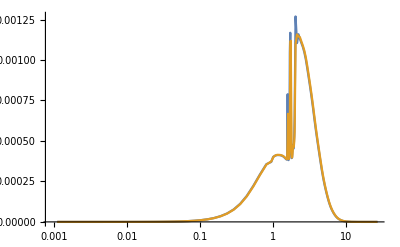

```mathematica
ListLogLinearPlot[{spectrumNoV,spectrum},Joined->True]
```

```mathematica
spectrum[[nbins,2]]
```

3.1445×10^-13

```mathematica
Diff = Table[{spectrum[[i,1]],(spectrumNoV[[i,2]]-spectrum[[i,2]])/spectrum[[i,2]]},{i,1,nbins}]
```

{{0.0011086,0.0597835},{0.00136245,0.0208366},{0.0016744,0.0208349},{0.00205776,0.0208365},{0.00252895,0.020833},{0.00310802,0.0208262},{0.00381964,0.0208209},{0.00469423,0.020819},{0.00576912,0.0208133},{0.00709009,0.0208063},{0.00871355,0.0207977},{0.0107089,0.0207871},{0.013161,0.0209712},{0.0161745,0.0207586},{0.0198778,0.0207401},{0.0244291,0.0207146},{0.0300228,0.0206845},{0.0368973,0.0206478},{0.0453458,0.0206026},{0.0557286,0.0205469},{0.0684887,0.0204782},{0.0841708,0.0203969},{0.103445,0.0202908},{0.127129,0.020157},{0.156239,0.0199979},{0.192014,0.0197983},{0.235975,0.0195464},{0.290012,0.0192403},{0.35642,0.0187656},{0.438025,0.0176556},{0.538322,0.0155009},{0.661586,0.011912},{0.813071,0.00745767},{0.9494,-0.00882533},{1.00698,0.00956062},{1.02103,0.000806713},{1.03527,-0.00030249},{1.04972,-0.000556806},{1.06437,-0.000834779},{1.07922,-0.00117394},{1.09427,-0.00150525},{1.10957,-0.0018934},{1.12507,-0.00232886},{1.14077,-0.00280551},{1.15667,-0.00332495},{1.17282,-0.00353621},{1.18922,-0.0034338},{1.20582,-0.00340365},{1.22262,-0.00347264},{1.23967,-0.00358052},{1.25702,-0.00370661},{1.27457,-0.00398764},{1.29232,-0.00426217},{1.31037,-0.00444193},{1.32867,-0.00465926},{1.34722,-0.00490007},{1.36602,-0.00520591},{1.38507,-0.00554174},{1.40442,-0.00588642},{1.42407,-0.00624357},{1.44397,-0.00669525},{1.46411,-0.00712622},{1.48451,-0.00701629},{1.50521,-0.00667687},{1.52626,-0.00616659},{1.54756,-0.00518689},{1.56916,0.024365},{1.59106,0.538466},{1.61326,-0.335832},{1.63581,-0.139909},{1.65866,0.00188619},{1.68181,0.0954628},{1.70526,0.774718},{1.72906,0.155894},{1.75321,-0.219781},{1.77771,-0.444537},{1.80251,-0.123607},{1.82766,-0.00326699},{1.85321,0.0689327},{1.87906,0.0443631},{1.90525,-0.0306803},{1.93185,0.0331779},{1.95885,0.0592043},{1.98387,0.160886},{2.04176,0.156367},{2.13798,-0.04612},{2.23876,0.0113879},{2.34423,-0.00915494},{2.4547,-0.00778813},{2.57042,-0.00724512},{2.69154,-0.00889217},{2.81835,-0.0118013},{2.95122,-0.0144443},{3.09033,-0.0156376},{3.23594,-0.0162874},{3.38845,-0.0178635},{3.54816,-0.0201905},{3.71537,-0.0229308},{3.89047,-0.0233071},{4.07382,-0.0234198},{4.26582,-0.0248403},{4.46687,-0.0271872},{4.67736,-0.0299765},{4.8978,-0.0301447},{5.12864,-0.030126},{5.37033,-0.0315623},{5.62341,-0.0339838},{5.88844,-0.0368986},{6.16597,-0.0370817},{6.45654,-0.0371054},{6.76081,-0.0387663},{7.07947,-0.0414844},{7.41313,-0.0447198},{7.76249,-0.0451109},{8.1283,-0.0454519},{8.51134,-0.0475005},{8.91249,-0.0507008},{9.33253,-0.0545034},{10.1091,-0.0474072},{11.8629,-0.0737196},{14.579,-0.101598},{17.9172,-0.126047},{22.0199,-0.156419},{27.0616,-0.193274}}

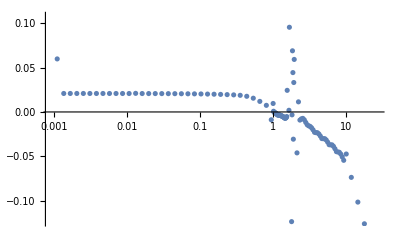

```mathematica
ListLogLinearPlot[Diff]
```

```mathematica
spectrumStationary=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[Iz[12,μ,T,0*5.994,1,4/10,Tval,dens]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->5, MaxRecursion->10,Method->"LocalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,nbins}]
```

{{0.0011086,1.26533×10^-9},{0.00136245,1.9109×10^-9},{0.0016744,2.88564×10^-9},{0.00205776,4.35662×10^-9},{0.00252895,6.57904×10^-9},{0.00310802,9.93456×10^-9},{0.00381964,1.50002×10^-8},{0.00469423,2.2646×10^-8},{0.00576912,3.41857×10^-8},{0.00709009,5.15987×10^-8},{0.00871355,7.78698×10^-8},{0.0107089,1.17499×10^-7},{0.013161,1.77211×10^-7},{0.0161745,2.6726×10^-7},{0.0198778,4.0292×10^-7},{0.0244291,6.07186×10^-7},{0.0300228,9.14495×10^-7},{0.0368973,1.37641×10^-6},{0.0453458,2.06997×10^-6},{0.0557286,3.10988×10^-6},{0.0684887,4.6665×10^-6},{0.0841708,6.99042×10^-6},{0.103445,0.000010455},{0.127129,0.0000155997},{0.156239,0.0000232102},{0.192014,0.0000344088},{0.235975,0.0000507827},{0.290012,0.000074545},{0.35642,0.000108529},{0.438025,0.000155375},{0.538322,0.000215343},{0.661586,0.0002823},{0.813071,0.000343998},{0.9494,0.000355854},{1.00698,0.00038503},{1.02103,0.000386823},{1.03527,0.000388447},{1.04972,0.000389934},{1.06437,0.000391251},{1.07922,0.00039238},{1.09427,0.000393301},{1.10957,0.000394},{1.12507,0.000394356},{1.14077,0.00039447},{1.15667,0.000394299},{1.17282,0.00039398},{1.18922,0.000393693},{1.20582,0.000393372},{1.22262,0.000392964},{1.23967,0.000392448},{1.25702,0.00039181},{1.27457,0.000390982},{1.29232,0.000389944},{1.31037,0.000388758},{1.32867,0.000387412},{1.34722,0.000385875},{1.36602,0.000384119},{1.38507,0.000382116},{1.40442,0.000379867},{1.42407,0.000377366},{1.44397,0.000374556},{1.46411,0.000371454},{1.48451,0.000368405},{1.50521,0.000365507},{1.52626,0.000362869},{1.54756,0.000360791},{1.56916,0.000377308},{1.59106,0.000759732},{1.61326,0.000417988},{1.63581,0.000356519},{1.65866,0.000363414},{1.68181,0.000427588},{1.70526,0.00101504},{1.72906,0.0011327},{1.75321,0.000841148},{1.77771,0.000410389},{1.80251,0.000366853},{1.82766,0.000368764},{1.85321,0.000417008},{1.87906,0.000446934},{1.90525,0.000422364},{1.93185,0.000450052},{1.95885,0.000495363},{1.98387,0.000614311},{2.04176,0.00122953},{2.13798,0.00106681},{2.23876,0.00112003},{2.34423,0.00109103},{2.4547,0.00106582},{2.57042,0.00104144},{2.69154,0.00100949},{2.81835,0.000966958},{2.95122,0.00091283},{3.09033,0.000855105},{3.23594,0.000796436},{3.38845,0.000734407},{3.54816,0.000667919},{3.71537,0.000597454},{3.89047,0.000531142},{4.07382,0.000469661},{4.26582,0.000410461},{4.46687,0.0003527},{4.67736,0.000296921},{4.8978,0.000248233},{5.12864,0.00020638},{5.37033,0.000169169},{5.62341,0.000135913},{5.88844,0.000106558},{6.16597,0.0000829148},{6.45654,0.0000640897},{6.76081,0.0000487193},{7.07947,0.0000361775},{7.41313,0.0000261255},{7.76249,0.0000186995},{8.1283,0.0000132735},{8.51134,9.23907×10^-6},{8.91249,6.25735×10^-6},{9.33253,4.10458×10^-6},{10.1091,2.1295×10^-6},{11.8629,4.02525×10^-7},{14.579,2.97616×10^-8},{17.9172,1.21984×10^-9},{22.0199,2.45061×10^-11},{27.0616,2.07417×10^-13}}

```mathematica
Export["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoV_124.csv",spectrumStationary]
```

/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoV_124.csv